```mathematica
(*Pure strategy equilibrium*)
Clear["Global`*"];
ClearAll;
```

```mathematica
(*Basics*)
```

```mathematica
(*main functions: c(e), profits *)
c[e_]:=e^2
profits[e_]:=probWin[e]*V-c[e]
```

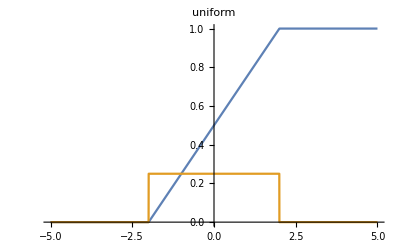
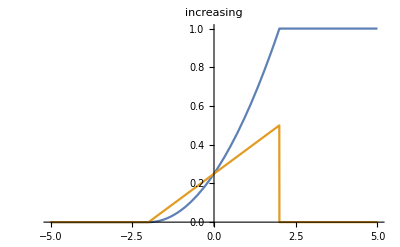
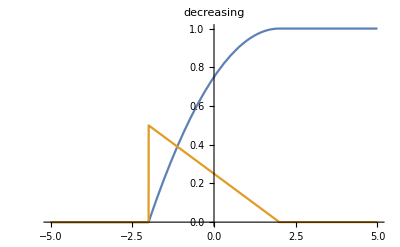

```mathematica
(*distribution functions *)
uniformCDF[x_]:=Piecewise[{{(x-a)/(b-a),a<x<b},{1, x>=b},{0,x<=a}}];
uniformPDF[x_]:= uniformCDF'[x];

increasingCDF[x_]:=Piecewise[{{((x-a)/(b-a))^2,a<x<b},{1, x>=b},{0,x<=a}}];
increasingPDF[x_]:=increasingCDF'[x];

decreasingCDF[x_]:=Piecewise[{{((a-x)(a+x-2b))/(b-a)^2,a<x<b},{1, x>=b},{0,x<=a}}];
decreasingPDF[x_]:=decreasingCDF'[x];
(*{decreasingPDF[x],increasingPDF[x],uniformPDF[x]}*)
a:=-2; (*Set values for plotting*)
b:=2;
p1=Plot[{uniformCDF[x],uniformPDF[x]},{x,-5,5}, PlotLabel->uniform];
p2=Plot[{increasingCDF[x],increasingPDF[x]},{x,-5,5}, PlotLabel->increasing];
p3=Plot[{decreasingCDF[x],decreasingPDF[x]},{x,-5,5}, PlotLabel->decreasing];
{p1,p2,p3}

(*Plot[{uniformpdf[x], uniformcdf[x]},{x,-10,10}]*)
```

```mathematica
Clear[a]; (*Clear these values that we had created just for the plots*)
Clear[b];
a:=-2;
b:=2;
```

```mathematica
(*Pure strategy equilibria candidate in Increasing distribution*)
(*Probabilities of winning and profits*)
probWin[e_]:=Integrate[(n-1)*pdf[x]*cdf[x]^(n-2)*pdf[y],{y,a,b},{x,a,e-eStar+y}, Assumptions-> { n> 1 &&b>0, a<0}]
(*probWin[eStar] (*test = 1/n*)*)
profits[e_]:=probWin[e]*V-c[e]
firstDerivative[e_]:=profits'[e]
secondDerivative[e_]:=profits''[e]

cdf[x_]:=increasingCDF[x];
pdf[x_]:=increasingPDF[x];
firstDerivativeEvaluatedAtEstar[e_]=Simplify[firstDerivative[e]/. e->eStar,Assumptions->{ n> 1 ,b>0, a<0}]; 
secondDerivativeEvaluatedAtEstar[e_]=Simplify[secondDerivative[e]/.e->eStar ,Assumptions->{ n> 1 ,b>0, a<0}];

increasingFOC:=Solve[firstDerivativeEvaluatedAtEstar[e]==0,eStar]
increasingSOC:=secondDerivativeEvaluatedAtEstar[e]<=0

{increasingFOC,increasingSOC}
```

{{{eStar→((-1+n) V)/(2 (-1+2 n))}},-2+1/8 (-3+2 n) V≤0}

```mathematica
(*Pure strategy equilibria candidate in Uniform distribution*)
cdf[x_]:=uniformCDF[x];
pdf[x_]:=uniformPDF[x];
firstDerivativeEvaluatedAtEstar[e_]=Simplify[firstDerivative[e]/. e->eStar,Assumptions->{ n> 1 &&b>0, a<0}]; (*Correct*)
secondDerivativeEvaluatedAtEstar[e_]=Simplify[secondDerivative[e]/.e->eStar ,Assumptions->{ n> 1 &&b>0, a<0}];(*Correct = e*=V/2*(b-a)*)

uniformFOC:=Solve[firstDerivativeEvaluatedAtEstar[e]==0,eStar]
uniformSOC:=secondDerivativeEvaluatedAtEstar[e]<=0

{uniformFOC,uniformSOC}
```

{{{eStar→V/8}},-2+1/16 (-1+n) V≤0}

```mathematica
(*Pure strategy equilibria candidate in Decreasing distribution*)
cdf[x_]:=decreasingCDF[x];
pdf[x_]:=decreasingPDF[x];
firstDerivativeEvaluatedAtEstar[e_]=Simplify[firstDerivative[e]/. e->eStar,Assumptions->{ n> 1 &&b>0, a<0}]; 
secondDerivativeEvaluatedAtEstar[e_]=Simplify[secondDerivative[e]/.e->eStar ,Assumptions->{ n> 1 &&b>0, a<0}];

decreasingFOC:=Solve[firstDerivativeEvaluatedAtEstar[e]==0,eStar]
decreasingSOC:=secondDerivativeEvaluatedAtEstar[e]<=0

{decreasingFOC,decreasingSOC}
```

{{{eStar→1/4 (1/(8 Gamma[2-n] Gamma[-1/2+n])ⅈ ⅇ^(-2 ⅈ n π) (-1+ⅇ^(2 ⅈ n π)) V Csc[n π] (-2 (-1)^n π^(3/2) Csc[n π]+2 (-1)^n n π^(3/2) Csc[n π]-2^n Cos[n π] Gamma[2-n] Gamma[-1/2+n] Hypergeometric2F1[2-n,-1+n,n,1/2])+1/(n (1+n))2^(-3+n) ⅇ^(-2 ⅈ n π) V (-n Hypergeometric2F1[2-n,-1+n,n,1/2]+ⅇ^(2 ⅈ n π) n Hypergeometric2F1[2-n,-1+n,n,1/2]-n^2 Hypergeometric2F1[2-n,-1+n,n,1/2]+ⅇ^(2 ⅈ n π) n^2 Hypergeometric2F1[2-n,-1+n,n,1/2]+8 ⅇ^(2 ⅈ n π) Hypergeometric2F1[2-n,n,1+n,1/2]-8 ⅇ^(2 ⅈ n π) n^2 Hypergeometric2F1[2-n,n,1+n,1/2]-4 ⅇ^(2 ⅈ n π) n Hypergeometric2F1[2-n,1+n,2+n,1/2]+4 ⅇ^(2 ⅈ n π) n^2 Hypergeometric2F1[2-n,1+n,2+n,1/2]))}},1/(16 n Gamma[2-n] Gamma[-1/2+n])(-1)^-n ⅇ^(ⅈ n π) (2 (-1+n) n π^(3/2) V Csc[n π]+Gamma[2-n] Gamma[-1/2+n] (-32 n+2^(1+n) n V Hypergeometric2F1[2-n,-1+n,n,1/2]-2^n (-1+n) V Hypergeometric2F1[2-n,n,1+n,1/2]))≤0}